# MATH 340: 23 September, 2019

## Reminder: Project topics and partners--you will get an email.

## Test 1 week from today! LATEX, Excel, and Mathematica.

## Buffy Worksheet Solutions

```mathematica
Clear["Global`*"]
```

```mathematica
system = {
H'[t]==(0.1)*H[t]*(1-H[t]/90000)-(1/300)*H[t]*V[t],
V'[t]==(1/300)*(1/240)*V[t]*H[t]-(2/3)*V[t]+(0.075)*V[t],
H[0]==38500,
V[0]==35
}
```

{H'[t]==0.1 (1-H[t]/90000) H[t]-1/300 H[t] V[t],V'[t]==-0.591667 V[t]+(H[t] V[t])/72000,H[0]==38500,V[0]==35}

```mathematica
answer=NDSolve[system,{H[t],V[t]},{t,0,100}]
```

{{H[t]→InterpolatingFunction[…][t],V[t]→InterpolatingFunction[…][t]}}

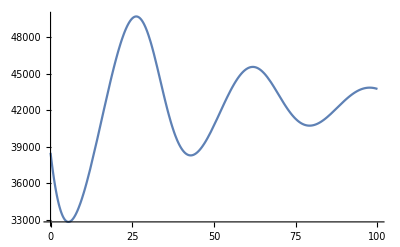

```mathematica
Plot[H[t]/.answer,{t,0,100}]
```

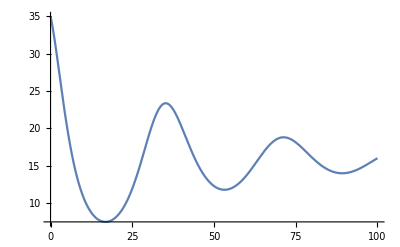

```mathematica
Plot[V[t]/.answer,{t,0,100}]
```

```mathematica
ParametricPlot[{Evaluate[H[t]]/.answer,Evaluate[V[t]]/.answer},{t,0,100}]
```

-Graphics-